```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

Updating from Wolfram Research server ...

Updating from Wolfram Research server ...

Updating from Wolfram Research server ...

«1 more identical outputs»

PacletInstall::lock: The paclet installation cannot proceed at this time because another paclet operation is being performed by a different instance of the Wolfram Language. Try the operation again.

Get::noopen: Cannot open CloudObject`.

Updating from Wolfram Research server ...

Updating from Wolfram Research server ...

Updating from Wolfram Research server ...

«1 more identical outputs»

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="/home/huangys/mount/DATA/Documents/2-d-data";}];
```

```mathematica
Kernel1[ϕn_][x_?NumberQ]:=NIntegrate[ϕn[p]/(p-x)^2,{p,0,1}];
Kernel2[ϕn_,ϕm_][x_?NumberQ,z_?NumberQ,ω_?NumberQ]:=NIntegrate[(ϕn[y]ϕm[z/ω y])/(y-x)^2,{y,0,1}];
```

```mathematica
A[ω_][ϕ1_,ϕ2_,ϕ3_]:=1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},Method->"GlobalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},Method->"GlobalAdaptive"](*r1=1*)
```

```mathematica
FBBplusDD[z_,ω_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=(1+ℂ)(-HeavisideTheta[ω-z](1-ω)/z NIntegrate[ϕ2[(1-ω)/(1-z)x]ϕ4[x](ϕ1[y]ϕ3[z/ω y])/(y-(1-(1-x)(1-ω)/z))^2,{x,0,1},{y,0,1}]+HeavisideTheta[z-ω](1-z)/ω NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1}])
```

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

```mathematica
ω[M1_,M2_,M3_]:=(*-*)(√((M1^2+M2^2-M3^2)^2-4 M1^2 M2^2))/(2 M1^2)+M2^2/(2 M1^2)-M3^2/(2 M1^2)+1/2
```

```mathematica
zfp[ω_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2-M3^2 ω+M4^2 ω))(M3^2+M1^2 ω-M2^2 ω-M3^2 ω+M4^2 ω-M1^2 ω^2+M2^2 ω^2-√(-4 (M3^2-M3^2 ω+M4^2 ω) (M1^2 ω-M1^2 ω^2)+(-M3^2-M1^2 ω+M2^2 ω+M3^2 ω-M4^2 ω+M1^2 ω^2-M2^2 ω^2)^2));
```

```mathematica
zfn[ω_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2-M3^2 ω+M4^2 ω))(M3^2+M1^2 ω-M2^2 ω-M3^2 ω+M4^2 ω-M1^2 ω^2+M2^2 ω^2+√(-4 (M3^2-M3^2 ω+M4^2 ω) (M1^2 ω-M1^2 ω^2)+(-M3^2-M1^2 ω+M2^2 ω+M3^2 ω-M4^2 ω+M1^2 ω^2-M2^2 ω^2)^2))
```

```mathematica
ASin[n_][m1_]:=
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
]
```

```mathematica
At[n_][ma_,mb_,δm_]:=Table[
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
],{m1,ma,mb,δm}]
```

```mathematica
B2toB0π0[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Set@@{Φπ[x_],ϕxπ};
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Set@@{Φπ[x_],ϕxπ};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.1,0.5,0.1}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.6,0.8,0.02}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.8,0.9,0.01}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.9,0.99,0.005}]
]
```

```mathematica
B2π2toB0π0[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Set@@{Φπ[x_],ϕxπ};
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Set@@{Φπ[x_],ϕxπ};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][Valsπ],ϕn[#][Φπ]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
ParallelTable[z=zfp[ω][M1,M2,M3,M4];If[z∈Reals,Print["z=",z,"    ω=",ω];{ω,FBBplusDD[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},],{ω,0.1,0.9,0.01}](*~Join~ParallelTable[Print["ω=",ω];{ω,FBBplusDD[ω][ϕ1,ϕ2,ϕ3,ϕ4]},{ω,0.6,0.8,0.02}]~Join~ParallelTable[Print["ω=",ω];{ω,FBBplusDD[ω][ϕ1,ϕ2,ϕ3,ϕ4]},{ω,0.8,0.9,0.01}]~Join~ParallelTable[Print["ω=",ω];{ω,FBBplusDD[ω][ϕ1,ϕ2,ϕ3,ϕ4]},{ω,0.9,0.99,0.005}]*)
]
```

#### Debug

```mathematica
Block[{mQ=√2000,mq=√0.3136},m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Φπ[x_]=ϕxπ;
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Φπ[x_]=ϕxπ;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][Valsπ],ϕn[#][Φπ]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];]
```

Wavefunction build complete.

```mathematica
zfp[0.5][M1,M2,M3,M4]
```

0.550383

```mathematica
FBBplusDD[zfp[0.5][M1,M2,M3,M4],0.5][ϕ1,ϕ2,ϕ3,ϕ4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.908458}. NIntegrate obtained -9.69675×10^281+2.70459×10^136 ⅈ and 1.35165×10^281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.899234}. NIntegrate obtained 1.50147×10^8 and 7.7809×10^7 for the integral and error estimates.

1.35018×10^8+0. ⅈ

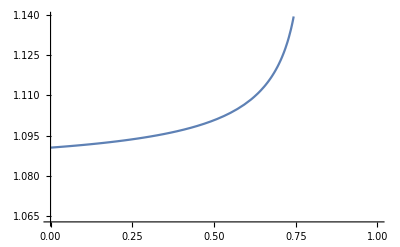

```mathematica
Plot[(zfp[x][M1,M2,M3,M4])/x,{x,0,1}]
```

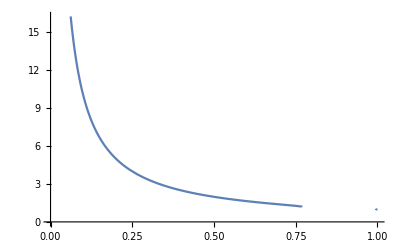

```mathematica
Plot[(zfn[x][M1,M2,M3,M4])/x,{x,0,1}]
```

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4]},(1+ℂ)(-HeavisideTheta[ω-z](1-ω)/z NIntegrate[ϕ2[(1-ω)/(1-z)x]ϕ4[x](ϕ1[y]ϕ3[z/ω y])/(y-(1-(1-x)(1-ω)/z))^2,{x,0,1},{y,0,1}]+HeavisideTheta[z-ω](1-z)/ω NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1}])]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.429446,0.505447}. NIntegrate obtained -2.1966165922340522940645389258927885619810148089581012431095580253×10^1510-5.2620286429825031327227159853958633720500447933640082518197173772×10^1116 ⅈ and 3.1572785222006068667743552541392232451608506631397822336978961747×10^1510 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.806499,0.995829857886447255589656979424262317479588091373443603515625}. NIntegrate obtained 860.196 and 941.808 for the integral and error estimates.

18.5365+0. ⅈ

```mathematica
Block[{ω=0.5,z=zfp[0.5][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.899234}. NIntegrate obtained 1.50147×10^8 and 7.7809×10^7 for the integral and error estimates.

1.50147×10^8

```mathematica
Block[{ω=0.5,z=zfp[0.5][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1},Method->"LocalAdaptive"]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.79153,0.812538}. NIntegrate obtained 0.281929 and 0.623145 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.791534,0.812538}. NIntegrate obtained 0.0916072 and 0.0854258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.791534,0.812541}. NIntegrate obtained 0.0295885 and 0.0310185 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

2.05784×10^12

```mathematica
Block[{ω=0.5,z=zfp[0.5][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1},Method->"MonteCarlo",MaxPoints->10^6]]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 180838. and 98458.6 for the integral and error estimates.

180838.

```mathematica
Block[{ω=0.5,z=zfp[0.5][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1},Method->"AdaptiveMonteCarlo",MaxPoints->10^6]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x,y} = {0.969608,0.972671}. NIntegrate obtained 570542. and 535375. for the integral and error estimates.

570542.

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4],x=0.5,λ=10^-4},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1-(1-x)(1-ω)/z-λ}]+NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,1-(1-x)(1-ω)/z+λ,1}]-2ϕ3[1-(1-x)(1-z)/ω] ϕ1[ω/z(1-(1-x)(1-z)/ω)]/λ]
```

0.989225

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.989164285334936}. NIntegrate obtained -13223.1 and 10510.5 for the integral and error estimates.

-13002.2

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4],x=0.5,λ=10^-4},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1-(1-x)(1-ω)/z-λ}]]
```

0.989225

9.60492×10^-7

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4],x=0.5,λ=10^-4},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,1-(1-x)(1-ω)/z+λ,1},MaxRecursion->20]]
```

0.989225

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in y near {y} = {0.989225426457066}. NIntegrate obtained -2.41435×10^7 and 1.68574×10^7 for the integral and error estimates.

-2.41435×10^7

0.989225

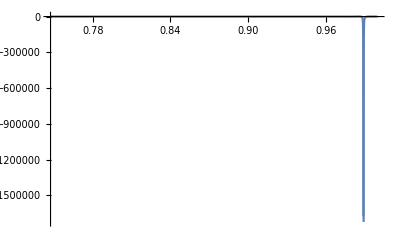

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4],x=0.5,λ=10^-4},Print[z];Plot[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,1-(1-x)(1-ω)/z+λ,1},PlotRange->All]]
```

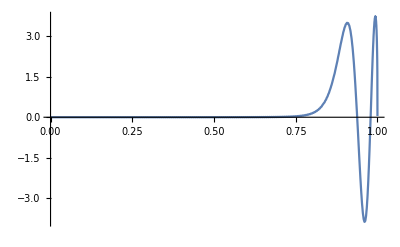

```mathematica
Plot[ϕ1[x],{x,0,1},PlotRange->All]
```

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4],x=0.5,λ=10^-4,y=0.99},Print[{ω,z,ω/z y}];(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2]
```

{0.5,0.989225,0.500391}

-18738.7

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4],x=0.5},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1-(1-x)(1-ω)/z,1},Method->{"PrincipalValue"}]]
```

0.989225

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.989386}. NIntegrate obtained -21594.5 and 19923.7 for the integral and error estimates.

-21594.5

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4],x=0.5},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1},Method->"LocalAdaptive"]]
```

0.989225

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.989225}. NIntegrate obtained -973.157 and 5.96569×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.989225}. NIntegrate obtained -876.1 and 6.29143×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.989225}. NIntegrate obtained -1001.86 and 8.52305×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-4.00256×10^8

```mathematica
Block[{ω=0.5,z=zfn[0.5][M1,M2,M3,M4],x=0.5},1-(1-x)(1-ω)/z]
```

0.747277

```mathematica
Block[{ω=0.},1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},Method->"GlobalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},Method->"GlobalAdaptive"]]
```